```mathematica
tmax=100;
tik = 60;

γ=.
ν=.
ψ=.
m=2.3;
G=m*9.8;
Ix=0.16;
Iy=0.14;
Iz=0.29;
P[δд_,Va_]:=(δд (-0.5884212317573334 Va+23.11936413533112 δд))2;
A1[γ_]:={{1,0,0},{0,Cos[γ],-Sin[γ]},{0,Sin[γ],Cos[γ]}};
A2[ν_]:={{Cos[ν],-Sin[ν],0},{Sin[ν],Cos[ν],0},{0,0,1}};
A3[ψ_]:={{Cos[ψ],0,Sin[ψ]},{0,1,0},{-Sin[ψ],0,Cos[ψ]}};
A[γ_,ν_,ψ_]:=A3[ψ].A2[ν].A1[γ];

схa[α_,β_,δг_,δв_]:=0.23+0.018*Abs[α]*180/π+0.01*Abs[β]*180/π+0.0005*Abs[δг]+0.0005*Abs[δв];
сya[α_,δг_]:=0.35+0.1*α*180/π-0.0005*δг;
сza[β_,δв_]:=-0.01*β*180/π-0.0005*δв;
mxa[δв_,δэ_,ωx_]:=0.001*δв+0.01*δэ-0.04*ωx;
mya[β_,δв_,ωy_]:=-0.003β*180/π+0.003*δв-0.04*ωy;
mza[α_,δг_,ωz_]:=-0.01-0.003α*180/π+0.01*δг-0.08*ωz;
```

```mathematica
Xa[α_,β_,δг_,δв_,Va_]:=схa[α,β,δг,δв]*0.02*Va^2*1.226;
Ya[α_,δг_,Va_]:=сya[α,δг]*0.15*Va^2*1.226;
Za[β_,δв_,Va_]:=сza[β,δв]*0.02*Va^2*1.226;

Mxa[δв_,δэ_,ωx_,Va_]:=mxa[δв,δэ,ωx]*1.8*0.02*Va^2*1.226;
Mya[β_,δв_,ωy_,Va_]:=mya[β,δв,ωy]*1.8*0.02*Va^2*1.226;
Mza[α_,δг_,ωz_,Va_]:=mza[α,δг,ωz]*1.8*0.02*Va^2*1.226;

X[α_,β_,δг_,δв_,Va_]:=-Xa[α,β,δг,δв,Va]*Cos[α]Cos[β]+Ya[α,δг,Va]*Sin[α]-Za[β,δв,Va]*Cos[α]Sin[β];
Y[α_,β_,δг_,δв_,Va_]:=Xa[α,β,δг,δв,Va]*Sin[α]Cos[β]+Ya[α,δг,Va]*Cos[α]-Za[β,δв,Va]*Sin[α]Sin[β];
Z[α_,β_,δг_,δв_,Va_]:=-Xa[α,β,δг,δв,Va]*Sin[β]+Za[β,δв,Va]*Cos[β];

Mx[α_,β_,δг_,δв_,δэ_,ωx_,ωy_,ωz_,Va_]:=Mxa[δв,δэ,ωx,Va]*Cos[α]Cos[β]+Mya[β,δв,ωy,Va]*Sin[α]-Mza[α,δг,ωz,Va]*Cos[α]Sin[β];
My[α_,β_,δг_,δв_,δэ_,ωx_,ωy_,ωz_,Va_]:=-Mxa[δв,δэ,ωx,Va]*Sin[α]Cos[β]+Mya[β,δв,ωy,Va]*Cos[α]-Mza[α,δг,ωz,Va]*Sin[α]Sin[β];
Mz[α_,β_,δг_,δв_,δэ_,ωx_,ωy_,ωz_,Va_]:=Mxa[δв,δэ,ωx,Va]*Sin[β]+Mza[α,δг,ωy,Va]*Cos[β];
```

{,,simspeed}

{,,Vв}

{,,αв}

------------------------------------------------------

{,,δд}

{,,δг}

{,,δв}

{,,δэ}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

UpT=False

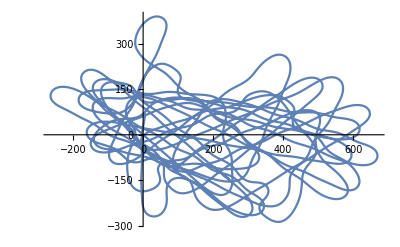

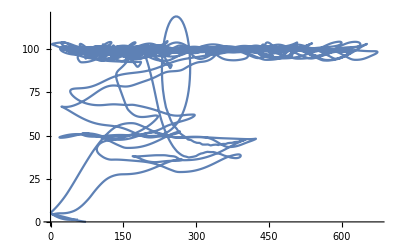

-Graphics3D-

```mathematica
time=60*120*10;
ksap=10;
γ=(0π)/180;ν=(0π)/180;ψ=(225π)/180;x=40;y=1.3;z=-40;Vx=-12;Vy=0;Vz=12;
ωx=0;
ωy=0;
ωz=0;
α=0;
β=0;

Dynamic[t]
simspeed=-10; {Slider[Dynamic[simspeed],{-10,10,1}],Dynamic[simspeed],"simspeed"}
Vв=0;{Slider[Dynamic[Vв],{0,14,0.1}],Dynamic[Vв],"Vв"}
αв=180;{Slider[Dynamic[αв],{0,360,1}],Dynamic[αв],"αв"}
Print["------------------------------------------------------"]
δд=1;{Slider[Dynamic[δд],{0,1,0.01}],Dynamic[δд],"δд"}
δг=0;{Slider[Dynamic[δг],{-10,10,0.1}],Dynamic[δг],"δг"}
δв=0;{Slider[Dynamic[δв],{-10,10,0.1}],Dynamic[δв],"δв"}
δэ=0;{Slider[Dynamic[δэ],{-10,10,0.1}],Dynamic[δэ],"δэ"}

cache={{x,y,z,ψ,ν,γ,0,0,0,0,0,0}};
tp=SessionTime[];
(*--------------------------------------------------------------------------------
константы*)
kPID=1;
Pд=0.5*kPID;Iд=0.01*kPID;Dд=0.04*kPID;
Pэ=0.6*kPID;Iэ=0.01*kPID;Dэ=0.5*kPID;
Pг=0.4*kPID;Iг=0.02*kPID;Dг=0.02*kPID;
Pв=-10*kPID;Iв=-1*kPID;Dв=-10*kPID;


Vsv=14;
Vpolet=20;
(*--------------------------------------------------------------------------------
переменные*)
Ztт=0;Ztп=0;
βт=0;βп=0;
dYmт=0;dYmп=0;
Vт=0;Vп=0;

Npoint=1;UpT=True;Ltarget=0;

vlet[ν,ψ,x,y,z];
sch=0;

For[t=0,t<=time,t++,
matrixA=A[γ,ν,ψ];
Va=√((Vx+Vв Sin[αв*π/180])^2+(Vy+Vв Cos[αв*π/180])^2+Vz^2);

If[Va>0,
VaV={Vx-Vв Cos[αв*π/180],Vy,Vz-Vв Sin[αв*π/180]};
Valoc=Transpose[matrixA].VaV;
α=ArcSin[(-Valoc[[2]])/(√(Valoc[[1]]^2+Valoc[[2]]^2))];
β=ArcSin[Valoc[[3]]/(√(Valoc[[1]]^2+Valoc[[2]]^2+Valoc[[3]]^2))];
];



axela=matrixA.{(P[δд,Va]+X[α,β,δг,δв,Va])/m,Y[α,β,δг,δв,Va]/m,Z[α,β,δг,δв,Va]/m }+{0,-9.8,0};
axelω={Mx[α,β,δг,δв,δэ,ωx,ωy,ωz,Va]/Ix-ωy ωz ((Iz-Iy)/Ix)
,My[α,β,δг,δв,δэ,ωx,ωy,ωz,Va]/Iy-ωz ωx ((Ix-Iz)/Iy),Mz[α,β,δг,δв,δэ,ωx,ωy,ωz,Va]/Iz-ωx ωy ((Iy-Ix)/Iz)};

ωx=ωx+axelω[[1]]/tik;
ωy=ωy+axelω[[2]]/tik;
ωz=ωz+axelω[[3]]/tik;

velE={(ωy Cos[γ]-ωz Sin[γ])/Cos[ν],ωy Sin[γ]+ωz Cos[γ],ωx-Tan[ν]*(ωy Cos[γ]-ωz Sin[γ])};

ψ=ψ+velE[[1]]/tik;
ν=ν+velE[[2]]/tik;
γ=γ+velE[[3]]/tik;


ν=Mod[ν,2π];
If[ν>π/2&&ν<(3π)/2,ν=π-ν;ψ=ψ+π;γ=γ+π];
If[ν>(3π)/2,ν=ν-2π];
ψ=Mod[ψ,2π];
γ=Mod[γ,2π];
If[γ>π,γ=γ-2π];


Vx=Vx+axela[[1]]/tik;
Vy=Vy+axela[[2]]/tik;
Vz=Vz+axela[[3]]/tik;

x=x+Vx/tik;
y=y+Vy/tik;
z=z+Vz/tik;



(*----------------------------------------------------------------------------------------------------------------*)
V=√(Vx^2+Vy^2+Vz^2);
αt=Mod[ArcSin[Vy/V],2π];
ϕt=Mod[If[Vx>=0,2π-ArcSin[Vz/√(Vx^2+Vz^2)],π+ArcSin[Vz/√(Vx^2+Vz^2)]],2π];

If[UpT &&Npoint==Length[trajup],
Npoint=1;
UpT=False;
Print["UpT=False"];
Ltarget=1;

traj2=twopointT[trajup[[-1,1]],trajup[[-1,3]],2π-trajup[[-1,4]],trajectory1[[1,1]],trajectory1[[1,3]],2π-trajectory1[[1,4]],Lgru];
For[j=Length[traj2],j>=1,j--,PrependTo[trajectory1,{traj2[[j,1]],Hud,traj2[[j,2]],2π-traj2[[j,3]],If[-traj2[[j,4]]<1000,-traj2[[j,4]]],0,9999,traj2[[j,5]]}]];

(*Break[];*)
];

If[Ltarget<1&&Length[trajectory1]>=Npoint+1,
If[UpT,
If[trajup[[Npoint+1,8]]!="U",
Npoint++
,

ϕpast=Abs[If[trajup[[Npoint,6]]-αt<=-π,2π+trajup[[Npoint,6]]-αt,If[trajup[[Npoint,6]]-αt>π,-2π+trajup[[Npoint,6]]-αt,trajup[[Npoint,6]]-αt]]];
ϕfuture=Abs[If[trajup[[Npoint+1,6]]-αt<=-π,2π+trajup[[Npoint+1,6]]-αt,If[trajup[[Npoint+1,6]]-αt>π,-2π+trajup[[Npoint+1,6]]-αt,trajup[[Npoint+1,6]]-αt]]];
If[ϕfuture<=ϕpast,Npoint++];
],

If[trajectory1[[Npoint+1,8]]!="T"&&trajectory1[[Npoint+1,8]]!="G"&&trajectory1[[Npoint+1,8]]!="NLT",
Npoint++,

If[trajectory1[[Npoint+1,8]]=="T",k=4;ϕN=ϕt,k=6;ϕN=αt];
ϕpast=Abs[If[trajectory1[[Npoint,k]]-ϕN<=-π,2π+trajectory1[[Npoint,k]]-ϕN,If[trajectory1[[Npoint,k]]-ϕN>π,-2π+trajectory1[[Npoint,k]]-ϕN,trajectory1[[Npoint,k]]-ϕN]]];
ϕfuture=Abs[If[trajectory1[[Npoint+1,k]]-ϕN<=-π,2π+trajectory1[[Npoint+1,k]]-ϕN,If[trajectory1[[Npoint+1,k]]-ϕN>π,-2π+trajectory1[[Npoint+1,k]]-ϕN,trajectory1[[Npoint+1,k]]-ϕN]]];
If[ϕfuture<=ϕpast,Npoint++];
]
];
];



If[If[UpT,trajup[[Npoint,7]]>1000,trajectory1[[Npoint,7]]>1000],αo=If[UpT,trajup[[Npoint,6]],trajectory1[[Npoint,6]]];
αdof=If[αo-αt<=-π,2π+αo-αt,If[αo-αt>π,-2π+αo-αt,αo-αt]];αadof=0;Laim=0];
If[If[UpT,trajup[[Npoint,5]]>1000,trajectory1[[Npoint,5]]>1000],ϕo=If[UpT,trajup[[Npoint,4]],trajectory1[[Npoint,4]]];
ϕdof=If[ϕo-ϕt<=-π,2π+ϕo-ϕt,If[ϕo-ϕt>π,-2π+ϕo-ϕt,ϕo-ϕt]];ϕadof=0;Laimxz=0];



If[If[UpT,trajup[[Npoint,8]]!="U",trajectory1[[Npoint,8]]!="T"&&trajectory1[[Npoint,8]]!="G"&&trajectory1[[Npoint,8]]!="NLT"],
xot=If[UpT,trajup[[Npoint,1]],trajectory1[[Npoint,1]]];
yot=If[UpT,trajup[[Npoint,2]],trajectory1[[Npoint,2]]];
zot=If[UpT,trajup[[Npoint,3]],trajectory1[[Npoint,3]]];
Laim=√((xot-x)^2+(yot-y)^2+(zot-z)^2);
Laimxz=√((xot-x)^2+(zot-z)^2);
αaim=ArcSin[(yot-y)/Laim];
ϕaim=Mod[If[xot-x>=0,2π-ArcSin[(zot-z)/Laimxz],π+ArcSin[(zot-z)/Laimxz]],2π];
If[αo-αaim<=-π,αadof=2π+αo-αaim,If[αo-αaim>π,αadof=-2π+αo-αaim,αadof=αo-αaim]];
If[ϕo-ϕaim<=-π,ϕadof=2π+ϕo-ϕaim,If[ϕo-ϕaim>π,ϕadof=-2π+ϕo-ϕaim,ϕadof=ϕo-ϕaim]];
];



Ltarget=If[If[UpT,trajup[[Npoint,8]]!="U",trajectory1[[Npoint,8]]!="T"&&trajectory1[[Npoint,8]]!="G"&&trajectory1[[Npoint,8]]!="NLT"],Laimxz*Cos[ϕadof],0];
Rxz=If[If[UpT,trajup[[Npoint,5]]>1000,trajectory1[[Npoint,5]]>1000],-30/Clip[ϕdof-Laimxz*Sin[ϕadof]/20,{-1,1}],-If[UpT,trajup[[Npoint,5]],trajectory1[[Npoint,5]]]];
Ry=If[If[UpT,trajup[[Npoint,7]]>1000,trajectory1[[Npoint,7]]>1000],30/Clip[(αdof-Laim*Sin[αadof]/30),{-1,1}],If[UpT,trajup[[Npoint,7]],trajectory1[[Npoint,7]]]];



If[!UpT&&trajectory1[[Npoint,8]]=="NLT",ar={-V^2/Ry*Sin[αt]*Cos[ϕt]*If[Abs[γ]>π/2,-1,1],9.8+V^2/Ry*Cos[αt]*If[Abs[γ]>π/2,-1,1],V^2/Ry*Sin[αt]*Sin[ϕt]*If[Abs[γ]>π/2,-1,1]},ar={V^2/Rxz*Sin[ϕt]-V^2/Ry*Sin[αt]*Cos[ϕt],9.8+V^2/Ry*Cos[αt],V^2/Rxz*Cos[ϕt]+V^2/Ry*Sin[αt]*Sin[ϕt]}];
arl=Transpose[matrixA].ar;



Vobj=If[trajectory1[[Npoint,8]]=="G"||trajectory1[[Npoint,8]]=="PG",Vsv-(Vpolet-Vsv)*(y/Hud),Vpolet];
Vт=Vт+V-Vobj;
If[Vт<-100,Vт=-100];If[Vт>15,Vт=15];
δд=-Pд*(V-Vobj)-Iд*Vт-Dд*(V-Vobj-Vп)*60;
If[δд<0,δд=0];If[δд>1,δд=1];
Vп=V-Vobj;
If[trajectory1[[Npoint,8]]=="TD",δд=0];



Ztт=Ztт+arl[[3]];
δэ=Pэ*arl[[3]]+Iэ*Ztт+Dэ*(arl[[3]]-Ztп)*60;
If[δэ<-10,δэ=-10];If[δэ>10,δэ=10];
Ztп=arl[[3]];



dYm=arl[[2]]-Y[α,β,δг,δв,Va]/m;
dYmт=dYmт+dYm;
δг=Pг*dYm+Iг*dYmт-Dг*(dYm-dYmп)*60;
If[δг<-10,δг=-10];If[δг>10,δг=10];
dYmп=dYm; 



βт=βт+β;
δв=Pв*β+Iв*βт+Dв*(β-βп)*60;
If[δв<-10,δв=-10];If[δв>10,δв=10];
βп=β; 


(*----------------------------------------------------------------------------------------------------------------*)
If[sch>=ksap,sch=0;AppendTo[cache,{x,y,z,ψ,ν,γ,t,α,β,ωx,αt,Ltarget,Rxz,Ry,Npoint,ϕfuture,ϕpast}],sch++];


If[y<0,y=0;Vy=0;ν=0;γ=0;Break[]];
]




ListLinePlot[Table[{cache[[tg,3]],cache[[tg,1]]},{tg,1,Length[cache]}]]
ListLinePlot[Table[{√(cache[[tg,1]]^2+cache[[tg,3]]^2),cache[[tg,2]]},{tg,1,Length[cache]}]]
ListLinePlot3D[Table[{cache[[tg,1]],cache[[tg,3]],cache[[tg,2]]},{tg,1,Length[cache]}],PlotRange->All,AspectRatio->Automatic]

Animate[
ListLinePlot[{{Cos[cache[[a,6]]+π]+(cache[[a,4]]*180)/π,Sin[cache[[a,6]]+π]+(cache[[a,5]]*180)/π},{(cache[[a,4]]*180)/π,(cache[[a,5]]*180)/π},{-Sin[cache[[a,6]]]+(cache[[a,4]]*180)/π,Cos[cache[[a,6]]]+(cache[[a,5]]*180)/π},{(cache[[a,4]]*180)/π,(cache[[a,5]]*180)/π},{Cos[cache[[a,6]]]+(cache[[a,4]]*180)/π,Sin[cache[[a,6]]]+(cache[[a,5]]*180)/π}},AspectRatio->Automatic],
{a,1,Length[cache],1},AnimationRunning->False]
```

```mathematica
gr1=ListLinePlot3D[Table[{cache[[tg,1]],cache[[tg,2]],cache[[tg,3]]},{tg,1,1Length[cache]}],PlotRange->All,AspectRatio->Automatic];
gr2=ListLinePlot3D[Table[{trajup[[tg,1]],trajup[[tg,2]],trajup[[tg,3]]},{tg,1,Length[trajup]}],PlotRange->All,AspectRatio->Automatic,PlotStyle->Red];
gr3=ListLinePlot3D[Table[{trajectory1[[tg,1]],trajectory1[[tg,2]],trajectory1[[tg,3]]},{tg,1,1Length[trajectory1]}],PlotRange->All,AspectRatio->Automatic,PlotStyle->Green];
Show[{gr1,gr2,gr3},PlotRange->All,BoxRatios->Automatic]


(*красное - траектория взлета, зеленая - расчетная траектория полета, синее - действительная траектория полета*)
```

-Graphics3D-